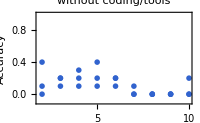

```mathematica
ListPlot[
{
{{2,0.4},{2,0.1},{2,0.},
{3,0.2},{3,0.1},{3,0.2},
{4,0.2},{4,0.1},{4,0.3},
{5,0.4},{5,0.1},{5,0.2},
{6,0.2},{6,0.2},{6,0.1},
{7,0.1},{7,0.},{7,0.},
{8,0.},{8,0.},{8,0.},
{9,0.},{9,0.},{9,0.},
{10,0.},{10,0.},{10,0.2}}
},
PlotRange->{All,{-0.1,1}},
FrameLabel->{"Length","Accuracy"},
ImageSize->200,
PlotLegends->Placed[{"ChatGPT-4o"},Right],
PlotMarkers->{"OpenMarkers",4},
PlotLabel->"without coding/tools"
]
```

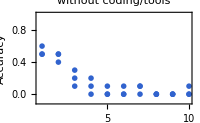

```mathematica
Block[{data},
data={{
{1,0.6},{1,0.5},{1,0.5},
{2,0.4},{2,0.5},{2,0.5},
{3,0.3},{3,0.1},{3,0.2},
{4,0.1},{4,0.2},{4,0.},
{5,0.1},{5,0.},{5,0.},
{6,0.1},{6,0.},{6,0.},
{7,0.1},{7,0.},{7,0.1},
{8,0.},{8,0.},{8,0.},
{9,0.},{9,0.},{9,0.},
{10,0.},{10,0.1},{10,0.}}};
ListPlot[
Mean[data],
PlotRange->{All,{-0.1,1}},
FrameLabel->{"Max length","Accuracy"},
ImageSize->200,
PlotLegends->Placed[{"ChatGPT-4o"},Right],
PlotMarkers->{"OpenMarkers",4},
PlotLabel->"without coding/tools"
]]
```

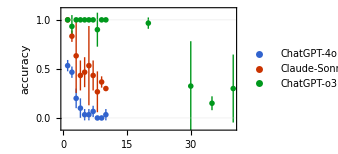

```mathematica
Block[{data,plot},
data=<|"ChatGPT-4o"->{
{1,0.6},{1,0.5},{1,0.5},
{2,0.4},{2,0.5},{2,0.5},
{3,0.3},{3,0.1},{3,0.2},
{4,0.1},{4,0.2},{4,0.},
{5,0.1},{5,0.},{5,0.},
{6,0.1},{6,0.},{6,0.},
{7,0.1},{7,0.},{7,0.1},
{8,0.},{8,0.},{8,0.},
{9,0.},{9,0.},{9,0.},
{10,0.},{10,0.1},{10,0.}},
"Claude-Sonnet-4"->{
{1,1.},{1,1.},{1,1.},
{2,0.9},{2,0.8},{2,0.8},
{3,0.2},{3,0.9},{3,0.8},
{4,0.3},{4,0.4},{4,0.6},
{5,0.3},{5,0.6},{5,0.5},
{6,0.1},{6,0.9},{6,0.6},
{7,0.6},{7,0.4},{7,0.3},
{8,0.5},{8,0.2},{8,0.1},
{9,0.4},{9,0.4},{9,0.3},
{10,0.3},{10,0.3},{10,0.3}},
"ChatGPT-o3"->{
{1,1.},{1,1.},{1,1.},
{2,0.8},{2,1.},{2,1.},
{3,1.},{3,1.},{3,1.},
{4,1.},{4,1.},{4,1.},
{5,1.},{5,1.},{5,1.},
{6,1.},{6,1.},{6,1.},
{7,1.},{7,1.},{7,1.},
{8,1.},{8,0.7},{8,1.},
{9,1.},{9,1.},{9,1.},
{10,1.},{10,1.},{10,1.},


{20,1.},{20,0.9},{20,1.},
{30,1.},{30,0.1},{30,0.2},
{35,0.2},{30,0.},{35,0.1},
{40,0.7},{40,0.1},{40,0.1}(*,
{100,0.},{100,0.}*)

}|>;
plot[score_]:=Block[{grp},
grp=GroupBy[score,First->Last];
grp=Around[Mean[#],StandardDeviation[#]]&/@grp;
(*ListPlot[,PlotRange->{All,{-0.1,1.1}},GridLines->{None,{0,1}},FrameLabel->{"\!\(N\)","accuracy"},ImageSize->200]*)
Table[{i,grp[i]},{i,Keys[grp]}]];
Block[{plots=plot/@data},
ListPlot[Table[plots[model],{model,Keys@plots}],PlotRange->{All,{-0.1,1.1}},GridLines->{None,{0,1}},FrameLabel->{"\!\(N\)","accuracy"},PlotMarkers->{"OpenMarkers",4},PlotLegends->Placed[(Style[#,"Text"]&/@Keys@plots),Right],ImageSize->250]]
]
```